# HyperBloch package tutorial

## Coherent sequences

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch coherent sequences tutorial on the HyperCells&HyperBloch website. In this tutorial, the import of adjacency matrices that capture the normal subgroup relations between pairwise distinct translation groups of corresponding triangle group quotients (constructed through HyperBloch’s sister package HyperCells) and the construction of normal subgroup tree graphs is showcased. In addition, coherent sequences of normal subgroups are visualized and determined through the built-in Mathematica functions.

## Preliminaries:

### Remarks:

Before using the notebook to the Coherent sequences tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcqs file is in the current directory:

(2,8,8)-adjMat-BBG_66_sparse.hcqs

In case no such file exist in your current directory, please follow the instructions in the HyperBloch coherent sequences tutorial,  or download the file there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells file remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Normal subgroup tree graphs

### Import quotient sequences adjacency matrix

The quotient sequences adjacency matrix can be imported analogously to cell, model and supercell model graphs. The Import function is used to read the file, while the ImportQuotientSequencesAdjMatString function is used to parse the string and construct the adjacency matrix:

```mathematica
qsAdjMat=ImportQuotientSequencesAdjMatString[Import["(2,8,8)-adjMat-BBG_66_sparse.hcqs"]];
```

### Extract the adjacency matrix:

The adjacency matrix describing the normal subgroup relation between pairwise distinct translation groups Γ^(m), associated with corresponding triangle group quotients Δ/Γ^(m), can be extracted by using the string “AdjacencyMatrix” as a key:

```mathematica
qsAdjMat["AdjacencyMatrix"]
```

SparseArray[…]

### Visualize the normal subgroup tree graph:

#### Introduction:

Normal subgroup tree graphs can be visualized with the high-level visualization function VisualizeQuotientSequences. It is convenient to first consider a subgraph with genera of compactified unit cells up to genus 30, which provides an overseeable example. We can achieve this by passing a function to the option VertexFilter, which takes quotient names Tg.n of the form {g, n} as arguments and returns a boolean:

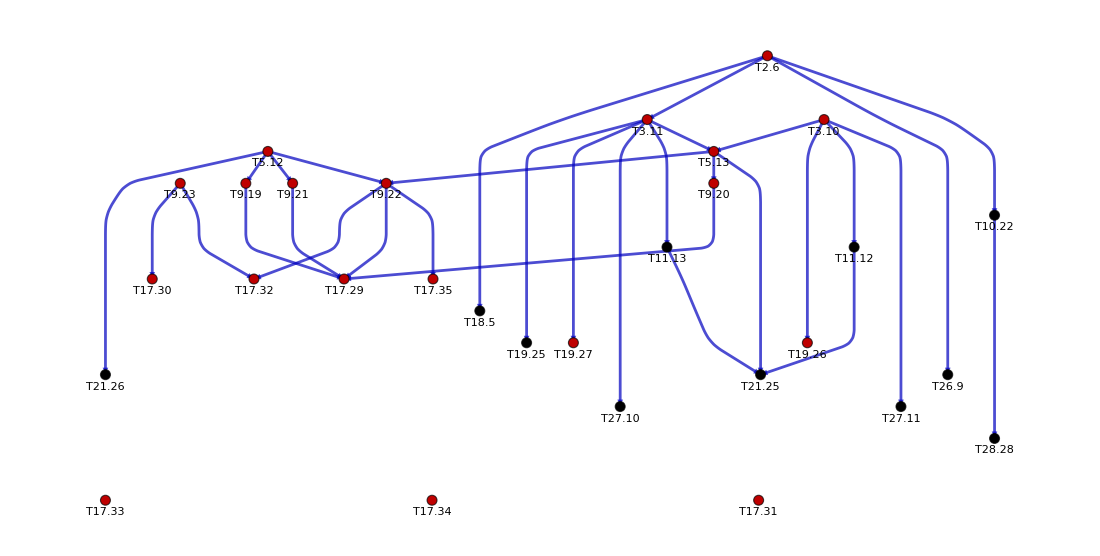

```mathematica
VisualizeQuotientSequences[qsAdjMat,
EdgeArrowSize->0.01, ImageSize->1100,VertexFilter->(#[[1]]<30&),
VertexLabelStyle->Directive[Black,Italic,15] ]
```

Every vertex corresponds to a translation group Γ^(m) associated with a corresponding unit cell and denoted with the label of the triangle group quotient Δ/Γ^(m),  with quotients in the tabulated list of quotients by Marston Conder. Each  Γ^(m) is a normal subgroup of Δ. Vertices highlighted in red indicate that the corresponding unit cell can be assembled mirror symmetrically with Schwarz triangles. Black vertices do not admit a mirror-symmetric unit cell, which limits some of the functionality of HyperCells package for them, namely those functions that construct or rely on symmetric cells (but not those working with generic supercells). Pairwise distinct vertices  Γ^(m),  Γ^(m+1) connected by a directed edge obey the normal subgroup relation Γ^(m) ⊳ Γ^(m+1).

#### Visualizing coherent sequences of normal subgroups:

Let us visualize the entire normal subgroup tree graph. We choose to emphasize the vertices associated with compactified unit cells of lower genera. This can be achieved by passing a function to the option LayerDistributionFunction, which distributes the layers of distinct genera in a desired way. In addition, we try avoid overlapping vertex labels by placing the labels alternately above and below the vertices of the tree graph:

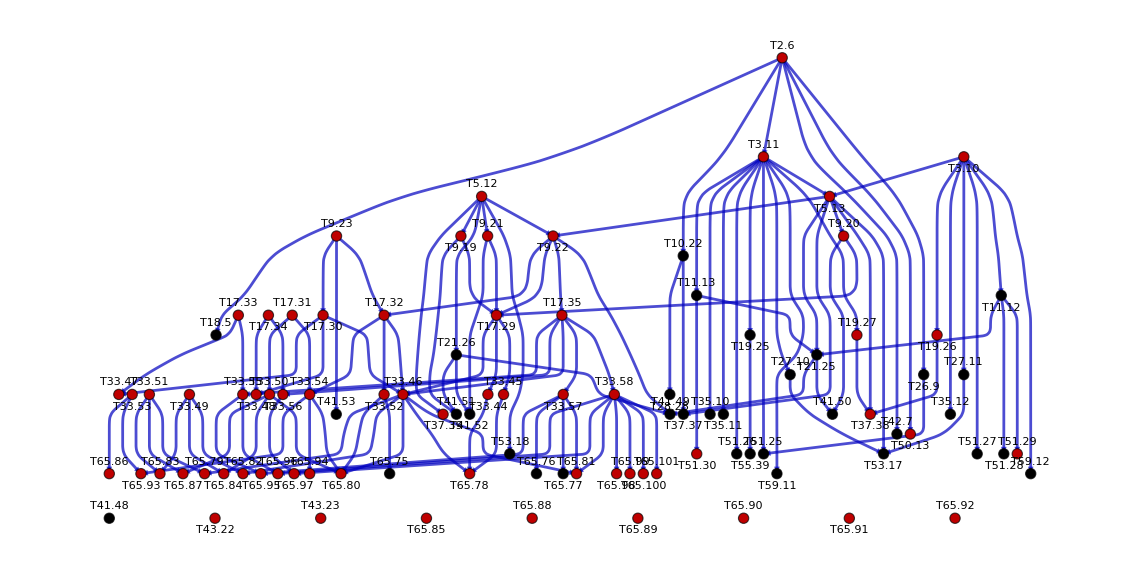

```mathematica
VisualizeQuotientSequences[qsAdjMat,
EdgeArrowSize->0.01,ImageSize->1140, 
LayerDistributionFunction->(6.5Log[#]&),
VertexLabelPlacement->"Alternate"]
```

Let us highlight the supercell sequence we have previously determined in GAP. This can be achieved with the option VertexFilterand HighlightSubgraph set to True:

```mathematica
keepVertices = {{2,6},{3,11},{5,13},{9,20},{17,29},{33,44}, {65,78}};
```

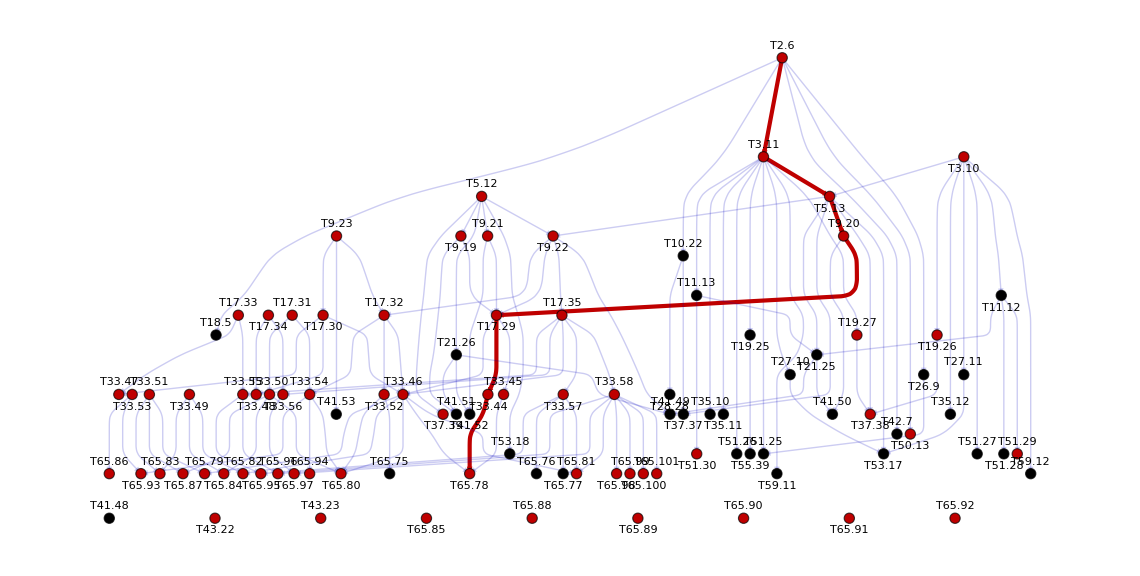

```mathematica
VisualizeQuotientSequences[qsAdjMat,
EdgeArrowSize->0.01,EdgeStyle->Directive[Darker[Blue, 0.25],Thick, Opacity[0.2]], 
HighlightSubgraph->True,ImageSize->1140,LayerDistributionFunction->(6.5Log[#]&),
VertexFilter->(MemberQ[keepVertices, #]&),VertexLabelPlacement->"Alternate"]
```

### Determine coherent sequences:

#### Preliminaries:

We can determine supercell sequences through the built-in Mathematica functions, such as FindPath or the resource function FindLongestPath, etc.. Let us reconstruct the sequences we have considered in the HyperBloch Supercells tutorial (where we adopt the sequence labels introduced in said tutorial):

```mathematica
fullGraph=VisualizeQuotientSequences[qsAdjMat, LayerDistributionFunction->(6.5Log[#]&),
 EdgeArrowSize->0.01,ImageSize->1140,VertexLabelPlacement->"Alternate"];
```

#### Supercell sequence 1:

The initial and the final vertex in the first supercell sequence are:

```mathematica
initialVertex={2,6};
finalVertex = {65,78};
```

FindPath can be used to determine all sequences that connect the initial with the final vertex:

```mathematica
sq1Lst = FindPath[fullGraph, initialVertex, finalVertex, Infinity,All];
```

The last sequence corresponds to the sequence we have previously considered:

```mathematica
sq1=sq1Lst[[-1]]
```

{{2,6},{3,11},{5,13},{9,20},{17,29},{33,44},{65,78}}

#### Supercell sequence 1A:

The initial and the final vertex in the next supercell sequence are:

```mathematica
initialVertex={3,10};
finalVertex = {65,81};
```

All sequences that connect the initial with the final vertex:

```mathematica
sq1ALst = FindPath[fullGraph, initialVertex, finalVertex, Infinity,All];
```

The last sequence corresponds to the sequence we have previously considered:

```mathematica
sq1A=sq1ALst[[1]]
```

{{3,10},{5,13},{9,22},{17,35},{33,58},{65,81}}

#### Supercell sequence 2A:

The initial and the final vertex in the next supercell sequence are:

```mathematica
initialVertex={5,12};
finalVertex = {65,79};
```

All sequences that connect the initial with the final vertex:

```mathematica
sq2ALst = FindPath[fullGraph, initialVertex, finalVertex, Infinity,All];
```

The second sequence corresponds to the sequence we have previously considered:

```mathematica
sq2A=sq2ALst[[2]]
```

{{5,12},{9,22},{17,32},{33,46},{65,79}}

### Highlight multiple coherent sequences (bonus):

We can use the  VisualizeQuotientSequences function to highlight multiple coherent sequences in the full normal subgroup tree graph. In order to avoid the inclusion of superfluous edges, we can use the option EdgeFilter instead of VertexFilter.

The corresponding edges are easily constructed:

```mathematica
sequnceLst={sq1, sq1A,sq2A};
edgeLst=Table[DirectedEdge[sequnceLst[[i,j]],sequnceLst[[i,j+1]]],{i,3},{j, Length[sequnceLst[[i]][[2;;]]]}];
allEdges=Flatten[edgeLst,1];
```

Let us highlight the three sequences by specifying three color maps:

```mathematica
cfunc=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[3]/3));
colorTables=Flatten[Table[
Style[edgeLst[[i,j]],Directive[cfunc[[i]], AbsoluteThickness[4]], Opacity[1]],
{i,3},{j,Length@edgeLst[[i]]}],1];
```

Therefore:

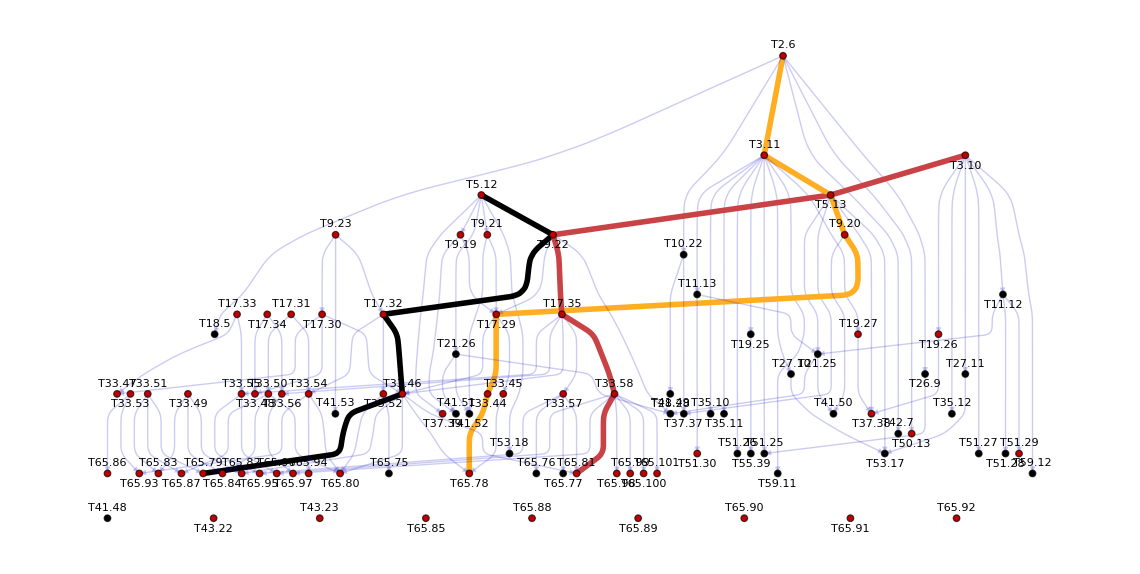

```mathematica
VisualizeQuotientSequences[qsAdjMat,
EdgeArrowSize->0.01,EdgeFilter->(MemberQ[allEdges,#]&),
EdgeStyle->Directive[Darker[Blue, 0.25],Thick, Opacity[0.2]],
HighlightSubgraph->True,HighlightSubgraphEdgeStyle->colorTables,
ImageSize->1140,LayerDistributionFunction->(6.5Log[#]&),
VertexSize->0.5,VertexLabelPlacement->"Alternate"]
```

```mathematica
NotebookSave[]
```